## How are symbols evaluated

Suppose we start with an undefined symbol

```mathematica
x
```

x

We can assign a value to this symbol using = (Set)

```mathematica
x=Random[]
```

0.795612

How does Mathematica know to replace every instance of x with its value?

It uses a global look-up table. We can find the rules for evaluating symbols by calling OwnValues

```mathematica
OwnValues[x]
```

{HoldPattern[x]:>0.795612}

The symbol :> (typed :>) means replace the lhs with the rhs, and only then evaluate the rhs

HoldPattern is a way of expressing a rule for a symbol without having the symbol transformed by other existing rules

```mathematica
y:=Random[]
```

```mathematica
OwnValues[y]
```

{HoldPattern[y]:>Random[]}

Since we used SetDelayed, we see that in this case y is replaced by a new random number each time

## How functions are evaluated

Recall our Fibonacci sequence

```mathematica
fib[0]:=0
fib[1]:=1
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
OwnValues[fib]
```

{}

fib has no OwnValues. That’s because if we evaluate

```mathematica
fib
```

fib

no rule is applied. Rules are only applied if we give an argument to fib

```mathematica
fib[5]
```

5

These kinds of rules (that require arguments) are known as DownValues

```mathematica
DownValues[fib]
```

{HoldPattern[fib[0]]:>0,HoldPattern[fib[1]]:>1,HoldPattern[fib[n_]]:>fib[n-1]+fib[n-2]}

The order of these rules shows the order in which Mathematica will attempt to apply them

There are also UpValues and SubValues, but they are a bit obscure...

## Understanding function evaluation

Trace helps us understand the order in which Mathematica evaluates expressions

```mathematica
Sin[Log[Exp[1],10/3]]
```

Sin[Log[10/3]]

```mathematica
Trace[Sin[Log[Exp[1],10/3]]]
```

{{{Exp[1],ⅇ},{{1/3,1/3},10/3,10/3},Log[ⅇ,10/3],Log[10/3]},Sin[Log[10/3]]}

Trace will not show the inner workings of all functions

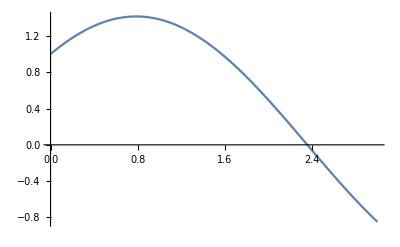

```mathematica
Plot[Sin[x]+Cos[x],{x,0,3}]
```

```mathematica
FindRoot[Sin[x]+Cos[x],{x,2}]
```

{0.795612→2.35619}

```mathematica
Trace[FindRoot[Sin[x]+Cos[x],{x,2}]]
```

{FindRoot[Sin[x]+Cos[x],{x,2}],{Sin[x]+Cos[x],Cos[x]+Sin[x]},{{x}=.,{x=.},{x=.,Null},{Null}},{x→2.35619},{{x,0.795612},0.795612→2.35619,0.795612→2.35619},{0.795612→2.35619}}

However, FindRoot supports EvaluationMonitor

```mathematica
FindRoot[Sin[x]+Cos[x],{x,2},EvaluationMonitor:>Print[x]]
```

2.

2.37206

2.35619

2.35619

{0.795612→2.35619}